# Cosmic History of Exotic Sectors and Resulting Gravitational Wave Signatures - Close Exotic Sector - document 4

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
```

## Input Parameters

Note: Work in GeV unless otherwise noted.

#### NNaturalness

```mathematica
MPl = 10^18; (*Planck Mass*)
mh0 = 88; (*Mass parameter of our Higgs*)
mReheaton = 100;(*Reheaton mass*)
tempReheat = 100;
gStarUsRH = 95.25 ;(*Above 125 Gev, 96.25; below 91 Gev, 92.25; below 80 Gev, 86.25*)
numSectors = 10000;
r = 1; (*Fine tuning of the spacing between our sector and others*)
quadCutOff =N[ mh0*Sqrt[numSectors/r]]
mHE[j_] =Sqrt[2]* (Sqrt[-((88^2)/r)(2*(-j) +r)]-30); (*Exotic Higgs mass for sector j, GeV - adjusted for a close exotic sector*)
FermionEMass[mHei_,LambdaQCD_,smQM_]:= (smQM/246000)(173000/246000)(LambdaQCD^3/mHei^2); (*inputs and outputs in MeV*)
```

8800.

#### Exotic Cosmology

```mathematica
h=0.71;
Gn =6.672*10^(-39); (*GeV^(-2)*)
ρc = 8.0962*h^2*10^(-47);(*GeV^(-4)*)
CurrentHR = 2.13*h*10^(-42)(*Sqrt[(8Pi/3)*Gn*ρc]*)(*GeV*)
qcdPT = 0.0906; (*GeV*)
TnucE = qcdPT*(102.75/56.75)^(1/3) (*By entropy conservation before and after the QCD PT, the final term is g_(*S) before and after PT*)
```

1.5123×10^-42

0.110425

## Particle Physics

This is the result of my calculations of decay width comparisons between exotic sectors and our own sector

```mathematica
edRatioForm =Times[2675.3151322890435,Power[Plus[Times[52.417199999999994,Power[Plus[1,Times[-69.88959999999999,Power[mr,-2]]],Rational[3,2]]],Times[3.1684,Power[Plus[1,Times[-12.6736,Power[mr,-2]]],Rational[3,2]]],Times[4.9923,Power[Plus[1,Times[-6.6564000000000005,Power[mr,-2]]],Rational[3,2]]]],-1],Power[mr,-6],Power[Plus[Power[mr,2],Times[-4,Power[m1,2],Power[ArcTan[Times[mr,Power[Plus[Times[4,Power[m1,2]],Times[-1,Power[mr,2]]],Rational[-1,2]]]],2]]],2]]
```

(2675.32 (mr^2-4 m1^2 ArcTan[mr/(√(4 m1^2-mr^2))]^2)^2)/((52.4172 (1-69.8896/mr^2)^(3/2)+3.1684 (1-12.6736/mr^2)^(3/2)+4.9923 (1-6.6564/mr^2)^(3/2)) mr^6)

```mathematica
edRatio[mE_]=edRatioForm/.mr-> mReheaton /. m1 -> mE
```

4.4575×10^-11 (10000-4 mE^2 ArcTan[100/(√(-10000+4 mE^2))]^2)^2

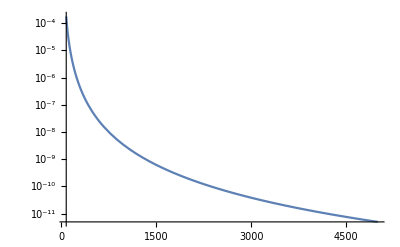

```mathematica
LogPlot[edRatio[x],{x,75,5000}]
```

```mathematica
edRatio[125]
```

0.0000152094

## Energy Densities, Entropy, and Temperature

```mathematica
ED[g_,T_] := (Pi^2/30)*g*T^4
T[g_,ED_]:= ((30/Pi^2)*ED/g)^(1/4)
S[g_,T_] := (2*Pi/45)*g*T^3
```

#### Reheating Values

```mathematica
aReheat = (3.909/gStarUsRH)^(1/3)*((0.24*10^(-12))/tempReheat) (*Here Subscript[a, 0] is taken to be 1 and current cosmic temp is 0.24 meV - taken from Daniel D Baumann Cambridge thermal notes chapter 3*)
edUsReheat = ED[gStarUsRH,tempReheat]
```

8.27837×10^-16

3.1336×10^9

```mathematica
noPT =ED[102.75,0.0906](*PT happens at 90.6 MeV*)
```

0.00227758

Note: when the exotic sector energy density drops below 0.00227758 GeV^4 then we get no phase transition

```mathematica
edEReheat = edUsReheat*edRatio[124.45]
```

48592.1

```mathematica
TEReheat=T[102.75,edEReheat](*Will always have a g of 102.75, otherwise you don't get a phase transition*)
```

6.15746

#### Phase transition values

```mathematica
aPT = (102.75/102.75)^(1/3)*(TEReheat/0.0906)*aReheat (*I'm going to assume that the GW is produced at close to the time of the PT*)
```

5.62624×10^-14

```mathematica
gstarSM=86.25;
TPTUs = (1/aPT)(3.909/gstarSM)^(1/3)*(0.24*10^(-12))(*This only works for the first ~150 sectors where our sector has frozen out Ws, the 86.25 needs to be adjusted beyond this - the next few lines will fix that*)
```

1.52088

```mathematica
If[TPTUs < 80.4, {TPTUs = TPTUs,gstarSM=gstarSM},{TPTUs =TPTUs*(86.25/92.25)^(1/3),gstarSM=92.25}]
```

{1.52088,86.25}

```mathematica
If[TPTUs < 91.2, {TPTUs = TPTUs,gstarSM=gstarSM},{TPTUs =TPTUs*(92.25/95.25)^(1/3),gstarSM=95.25}]
```

{1.52088,86.25}

```mathematica
ξh = TnucE/TPTUs
```

0.0726058

```mathematica
ρR=(Pi^2/30)((gstarSM/ξh^4)+ 56.75)*TnucE^4(*The 56.75 is our value of gh*)
```

151.82

```mathematica
HubbleRate=Sqrt[(8Pi/3)Gn*ρR]
```

2.91307×10^-18

```mathematica
strongStuff = 27130.4; (*Set so first phase transition has a 0.1 strength factor*)
α=strongStuff/ρR
```

178.702

```mathematica
RedShift = (aPT/1)^4 * (HubbleRate/CurrentHR)^2
```

0.000037179

#### Scalar field waves

Note: Assuming that the strength of the first PT is 0.1, we end up with completely negligible contributions from sound waves and turbulence

```mathematica
κ = 1;
vw = 1;
Δ = 0.11vw^3/(0.42+vw^2);
fp = 0.62*β/(1.8-0.1vw+vw^2);
s[f_]:=3.8(f/fp)^(2.8)/(1+2.8(f/fp)^3.8)
```

```mathematica
GWOriginal[f_,norm_,vFactor_,effFactor_,p_,q_,hob_,shapeFunction_,gwstr_]:=norm*vFactor*((effFactor*gwstr)/(1+gwstr))^(p)(hob)^q *shapeFunction
```

```mathematica
(*GWSFOriginal[f_, := GWOriginal[f*)
```

```mathematica
stream=OpenAppend["GWInputsCES.txt",FormatType->StandardForm];
Write[stream, "Sector   EDRH    TRH    TUTUs    rhoR    RedShift" ];
stream2=OpenAppend["GWInputsForDylanCES.txt",FormatType->StandardForm];
Write[stream2, "Sector  TUTUs(GeV)   gstarSM   Mass^2Sum(MeV^2)" ];
stream3=OpenAppend["GWAlphaInfCES.txt",FormatType->StandardForm];
Write[stream3, "Sector  topmass(eV)  tbpionmass(MeV)  AlphaInf" ];
```

```mathematica
(*titleLine = "Sector  EDRH   TRH   aPT   TUTUs   xih   rhoR   RedShift" ;
titleLine >>"GWInputs.txt"*)
```

```mathematica
SectorXValues[x_]:=Module[{k = x},
(*Particle Physics Stuff*)
mhe = N[mHE[k]];
mtop =FermionEMass[(mhe*1000/Sqrt[2]),90.6,173000]; (*Inputs and outputs in MeV*)
mbottom =FermionEMass[(mhe*1000/Sqrt[2]),90.6,4180];(*Inputs and outputs in MeV*)
mtbpion = Sqrt[(mbottom+mtop)/((2.3+4.8))]*(135); (*MeV output*)


EDRHk = edUsReheat*edRatio[mhe];
TRHk=T[102.75,EDRHk];
aPTk = (102.75/102.75)^(1/3)*(TRHk/0.0906)*aReheat ;
gstarSM=86.25;
TPTUsk = (1/aPTk)(3.909/gstarSM)^(1/3)*(0.24*10^(-12));
If[TPTUsk < 80.4, {TPTUsk = TPTUsk,gstarSM=gstarSM},{TPTUsk =TPTUsk*(86.25/92.25)^(1/3),gstarSM=92.25}];
If[TPTUsk < 91.2, {TPTUsk = TPTUsk,gstarSM=gstarSM},{TPTUsk =TPTUsk*(92.25/95.25)^(1/3),gstarSM=95.25}];xihk = TnucE/TPTUsk;
rhoRk=(Pi^2/30)((gstarSM/xihk^4)+ 56.75)*TnucE^4;
HRk=Sqrt[(8Pi/3)Gn*rhoRk];
RedShiftk = (aPTk/1)^4 * (HRk/CurrentHR)^2;

alphaInf = (TnucE^2/rhoRk)*(12/24)(mtbpion/1000)^2;(*mtbpion is in MeV, and is converted to GeV - the 12 is for the 12 pions involving the heavier top quark*)

Write[stream,k," ",EDRHk, " ", TRHk(*, " ", FortranForm[aPTk]*)," ", TPTUsk, " ",FortranForm[rhoRk]," ",RedShiftk ];
Write[stream2,k,"    ",TPTUsk, "    ", gstarSM,"    ",((mtbpion^2)*12)];
Write[stream3,k,"     ",mtop*10^6,"      ", mtbpion, "    ", alphaInf];
If[Mod[k,100] == 0,Print[k]]]
```

```mathematica
For[x = 1,x<3000,x++,SectorXValues[x];If[EDRHk < 0.002277,Break[]]]
```

100

200

300

400

500

600

700

800

900

1000

1100

1200

1300

1400

1500

1600

1700

1800

1900

2000

2100

```mathematica
aPT
```

5.62624×10^-14

```mathematica
EngineeringForm[2.3382427452799223*^-14]
```

23.3824×10^-15

```mathematica
NumberForm[2.3382427452799223*^-14]
```

2.33824×10^-14